```mathematica
genSim[t_,nt_,q_,simNum_,S0_,Δ_,σ_,γ_,ϕ_]:=
Module[
{ωVal,
triggerMat,
timeLine,
len,
dt,
moSignals,
orderDepth,
priceMat,
cash,
inventory,
curInv,
curTime,
curDepth,
loFilled,
isMO,
filled
},

(*{ωVal,triggerMat}=fdmSolver[t,nt,q];*)
ωVal=mat3;
triggerMat=trigger;
timeLine=N@Subdivide[0,t,nt];
moSignals=findTrigger[triggerMat,timeLine];
orderDepth=optDepth[ωVal];
len=Length@timeLine;
dt=First@Differences@timeLine;


priceMat=With[{proc=TransformedProcess[S0+σ*(up[i]-down[i]),{up\[Distributed]PoissonProcess[γ],down\[Distributed]PoissonProcess[γ]},i]},Last@Transpose@#&/@Normal@RandomFunction[proc,{0,t,dt},simNum]];

cash=ConstantArray[0,{simNum,len}];
inventory=ConstantArray[0,{simNum,len}];

Do[
curInv=inventory⟦All,i⟧;
curDepth=Table[orderDepth⟦j,i⟧, {j,Evaluate[Min[#,q]&/@(curInv+1)]}];


loFilled= Table[RandomReal[1],simNum]<(λ*ⅇ^(-κ*curDepth)*dt)//Thread;
loFilled=loFilled&&(Thread[curInv≠q])//Thread;

isMO=moSignals⟦#⟧== timeLine⟦i⟧&/@(curInv+1);
isMO=isMO&&(Thread[curInv≠q])//Thread;

filled=loFilled||isMO//Thread;
Table[ If[filled[j],inventory⟦j, i⟧+=1;cash⟦j,i⟧+=priceMat⟦j,i⟧;];,{j,Length@filled}];

(*With[{c=cash⟦All,i⟧,p},MapThread[If[#1,#2+=1;#3+=#4;]&,{Evaluate[loFilled||isMO//Thread],curInv,cash⟦All,i⟧,priceMat⟦All,i⟧}]];*)
filled=loFilled&&(!isMO)//Thread;
Table[If[filled⟦j⟧,cash⟦j,i⟧-=curDepth⟦j⟧;];,{j,Length@filled}];
(*MapThread[If[#1,#2-=#3;]&,{Evaluate[loFilled&&!isMO//Thread],cash⟦All,i⟧,curDepth}];*)

filled=(!loFilled)&&isMO//Thread;
Table[If[filled⟦j⟧,cash⟦j,i⟧+=Υ;];,{j,Length@filled}];
(*MapThread[If[#1,#2+=Υ;]&,{Evaluate[!loFilled&&isMO//Thread],cash⟦All,i⟧}];*)

If[i+1≤len,
inventory⟦All,i+1⟧=inventory⟦All,i⟧;
cash⟦All,i+1⟧=cash⟦All,i⟧;];
,{i,1,len}];

(*{TemporalData[cash,{ timeLine}],TemporalData[inventory,{timeLine}]}*)
inventory
]
```

```mathematica
(*t_,nt_,q_,simNum_,S0_,Δ_,σ_,γ_,ϕ_*;Last@Transpose@#&/@*)
```

```mathematica
genSim[T,3000,Ν,1,100,Δ,σ,γ,ϕ]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
{test1,test2}=genSim[T,3000,Ν,1,100,Δ,σ,γ,ϕ]
```

{0.012901}

{0.0114778}

{0.0105028}

{0.01}

{0.01}

{0.01}

«3 more identical outputs»

{0.00997609}

{0.00953232}

{0.00910044}

{0.00868284}

{0.00828263}

{0.00790343}

{0.0074562}

{0.00676727}

{0.00607581}

{0.00538155}

{0.00468454}

{0.003985}

{0.00328308}

{0.00249125}

{0.00150474}

{0.000466514}

{-0.000602407}

{-0.00170573}

{-0.00284759}

{-0.00403276}

{-0.00526707}

{-0.0065578}

{-0.00803088}

{-0.00965395}

{-0.0113778}

{-0.0132032}

{-0.0151443}

{-0.0172172}

{-0.0194415}

{-0.02184}

{-0.0244403}

{-0.0272749}

{-0.0303815}

{-0.0337058}

{-0.0372453}

{-0.0409267}

{-0.0445789}

{-0.0478744}

{-0.0502733}

{-0.0510917}

{-0.0498093}

{-0.0464338}

{-0.0414874}

{-0.0356348}

{-0.0293873}

{-0.0230427}

{-0.016741}

{-0.0105315}

{-0.00458285}

{0.000973435}

{0.00610504}

{0.00939085}

{0.01}

{0.01}

{0.01}

«2 more identical outputs»

{0.00547421}

{-0.00928887}

{0.0022019}

{-0.0144287+0.0628319 ⅈ}

Less::nord: Invalid comparison with -0.342897+1.10284×10^-16 ⅈ attempted.

{0.0185307}

{0.00327974+0.0628319 ⅈ}

Less::nord: Invalid comparison with -0.141459+4.54966×10^-17 ⅈ attempted.

{0.0244743}

{0.00930927+0.0628319 ⅈ}

Less::nord: Invalid comparison with -0.104641+3.3655×10^-17 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{0.0276052}

{0.012362+0.0628319 ⅈ}

{0.0296179}

{0.0142156+0.0628319 ⅈ}

{0.028225}

{0.0133588+0.0628319 ⅈ}

{0.0287772}

{0.0141272+0.0628319 ⅈ}

{0.0300828}

{0.0146742+0.0628319 ⅈ}

{0.0311598}

{0.01507+0.0628319 ⅈ}

{0.0321835}

{0.0153885+0.0628319 ⅈ}

{0.0331683}

{0.015672+0.0628319 ⅈ}

{0.0313163}

{0.0130768+0.0628319 ⅈ}

{0.0151781}

{0.00510936+0.0628319 ⅈ}

{0.0706093}

{0.0744805+0. ⅈ}

{0.0521339}

{0.0473215+0. ⅈ}

{0.0485682}

{0.0430573+0. ⅈ}

{0.0472821}

{0.0415619+0. ⅈ}

{0.046787}

{0.04099+0. ⅈ}

{0.0466523}

{0.0408306+0. ⅈ}

{0.046706}

{0.040884+0. ⅈ}

{0.0458455}

{0.0400433+0. ⅈ}

{0.0447141}

{0.0389783+0. ⅈ}

{0.0452814}

{0.0395771+0. ⅈ}

{0.0458468}

{0.0401682+0. ⅈ}

{0.0463887}

{0.0407359+0. ⅈ}

{0.0469104}

{0.0412834+0. ⅈ}

{0.0474161}

{0.0418151+0. ⅈ}

{0.0479112}

{0.0423362+0. ⅈ}

{0.0484017}

{0.0428526+0. ⅈ}

{0.048894}

{0.0433703+0. ⅈ}

{0.0493942}

{0.0438949+0. ⅈ}

{0.0498969}

{0.0444203+0. ⅈ}

{0.0502948}

{0.0448397+0. ⅈ}

{0.050669}

{0.0452349+0. ⅈ}

{0.051032}

{0.0456165+0. ⅈ}

{0.0513814}

{0.0459823+0. ⅈ}

{0.0517152}

{0.0463303+0. ⅈ}

{0.0520321}

{0.0466596+0. ⅈ}

{0.0523315}

{0.0469698+0. ⅈ}

{0.0467786}

{0.041457+0. ⅈ}

{0.043319}

{0.0380837+0. ⅈ}

{0.0308473}

{0.0258353+0. ⅈ}

{0.0783402}

{0.0735697+0. ⅈ}

{0.0696838}

{0.0639228+0. ⅈ}

{0.0633196}

{0.0574405+0. ⅈ}

{0.0609407}

{0.0550422+0. ⅈ}

{0.0597383}

{0.0538411+0. ⅈ}

{0.0590442}

{0.0531553+0. ⅈ}

{0.0586149}

{0.0527372+0. ⅈ}

{0.05834}

{0.0524749+0. ⅈ}

{0.0581622}

{0.0523101+0. ⅈ}

{0.0580489}

{0.0522099+0. ⅈ}

{0.05798}

{0.052154+0. ⅈ}

{0.0579427}

{0.0521294+0. ⅈ}

{0.0579283}

{0.0521273+0. ⅈ}

{0.0579307}

{0.0521417+0. ⅈ}

{0.0579457}

{0.0521682+0. ⅈ}

{0.05797}

{0.0522037+0. ⅈ}

{0.0580013}

{0.0522458+0. ⅈ}

{0.0580379}

{0.0522928+0. ⅈ}

{0.0580783}

{0.0523432+0. ⅈ}

{0.0581216}

{0.052396+0. ⅈ}

{0.0581668}

{0.0524504+0. ⅈ}

{0.0582133}

{0.0525058+0. ⅈ}

{0.0582606}

{0.0525616+0. ⅈ}

{0.0583083}

{0.0526174+0. ⅈ}

{0.058356}

{0.0526729+0. ⅈ}

{0.0584034}

{0.0527279+0. ⅈ}

{0.0584504}

{0.0527821+0. ⅈ}

{0.0584967}

{0.0528353+0. ⅈ}

{0.0585422}

{0.0528875+0. ⅈ}

{0.0585868}

{0.0529386+0. ⅈ}

{0.0586304}

{0.0529883+0. ⅈ}

{0.0586729}

{0.0530368+0. ⅈ}

{0.0587143}

{0.0530838+0. ⅈ}

{0.0587544}

{0.0531295+0. ⅈ}

{0.0587933}

{0.0531736+0. ⅈ}

{0.0588309}

{0.0532163+0. ⅈ}

{0.0588671}

{0.0532574+0. ⅈ}

{0.058902}

{0.0532969+0. ⅈ}

{0.0589354}

{0.0533349+0. ⅈ}

{0.0587196}

{0.0531241+0. ⅈ}

{0.0587333}

{0.0531403+0. ⅈ}

{0.0587751}

{0.053186+0. ⅈ}

{0.0588142}

{0.0532291+0. ⅈ}

{0.0588511}

{0.0532697+0. ⅈ}

{0.0588857}

{0.053308+0. ⅈ}

{0.058918}

{0.0533439+0. ⅈ}

{0.058948}

{0.0533773+0. ⅈ}

{0.0589756}

{0.0534082+0. ⅈ}

{0.0590007}

{0.0534366+0. ⅈ}

{0.0590232}

{0.0534622+0. ⅈ}

{0.059043}

{0.053485+0. ⅈ}

{0.0590599}

{0.0535047+0. ⅈ}

{0.0590737}

{0.0535213+0. ⅈ}

{0.0590841}

{0.0535344+0. ⅈ}

{0.0590908}

{0.0535437+0. ⅈ}

{0.0590934}

{0.0535489+0. ⅈ}

{0.0590915}

{0.0535494+0. ⅈ}

{0.0590845}

{0.0535448+0. ⅈ}

{0.0590718}

{0.0535344+0. ⅈ}

{0.0590526}

{0.0535174+0. ⅈ}

{0.059026}

{0.053493+0. ⅈ}

{0.058991}

{0.0534601+0. ⅈ}

{0.0589465}

{0.0534176+0. ⅈ}

{0.0588915}

{0.0533645+0. ⅈ}

{0.0588249}

{0.0532998+0. ⅈ}

{0.0587464}

{0.0532231+0. ⅈ}

{0.0586571}

{0.0531355+0. ⅈ}

{0.0585608}

{0.0530408+0. ⅈ}

{0.0584673}

{0.0529487+0. ⅈ}

{0.0675334}

{0.0619945+0. ⅈ}

{0.100661}

{0.0951458+0. ⅈ}

{0.0382568}

{0.0329725+0. ⅈ}

{0.0221424}

{0.0166854+0. ⅈ}

{0.00658357}

{-0.0033142+0. ⅈ}

{-0.009}

{TemporalData[…],TemporalData[…]}

```mathematica
test1
```

{{0.0140235,0.0138401,0.0136606,0.0134849,0.0133133,0.0131456,0.0129818,0.0128221,0.0126665,0.0125149,0.0123674,2979,3.69289×10^-6,-0.00078433,-0.00272603,-0.0044371,-0.00593517,-0.00721792,-0.0082627,-0.00903396,-0.0094777,-0.00951075,-0.009},9,{1}}
 |  |  |  |

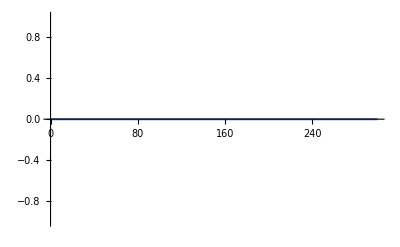

```mathematica
ListLinePlot@test1
```

```mathematica
pricePro=TransformedProcess[S0+σ*(up[t]-down[t]),{up\[Distributed]PoissonProcess[γ],down\[Distributed]PoissonProcess[γ]},t];
```

```mathematica
p=Last@Transpose@#&/@Normal@RandomFunction[pricePro,{0,T,dt},10];
```

```mathematica
p⟦All,4⟧
```

{100.,100.04,100.01,99.97,100.04,99.97,100.,100.01,99.97,99.99}